## Bh and NoBh Region for (α and Q space time parameters)

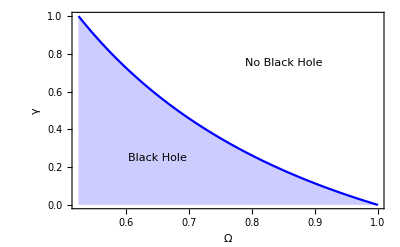

```mathematica
f[r_,Ω_,γ_] = 1-2/r(1+Ω/r^2+(Ω*γ)/r^3)^-1;
gg=Table[γ,{γ,0.,1,0.001}];
OO = Table[Ω/.FindRoot[{(f[r,Ω,γ]/.{γ->gg[[i]]})==0,D[(f[r,Ω,γ]/.{γ->gg[[i]]}),r]==0},{{r,1},{Ω,1}}],{i,1,Length[gg]}];
OOgg = Table[{OO[[i]],gg[[i]]},{i,1,Length[gg]}];

ListLinePlot[OOgg,Frame->True,FrameLabel->{"Ω","γ"},Filling->Axis,LabelStyle->Directive[FontFamily->"Times",FontSize->14,FontColor->Black],PlotRange->{{0.5229,1},{0,1}},PlotStyle->Blue,BaseStyle->{14,FontFamily->"Times"},
Epilog->{Text[Rotate[Framed["Black Hole",FrameStyle->None,Background->None],0Degree],{0.65,0.25}],Text[Rotate[Framed["No Black Hole",FrameStyle->None,Background->None],0Degree],{0.85,0.75}]}]
```

```mathematica
Ω/.FindRoot[{(f[r,Ω,γ]/.{γ->0.5})==0,D[(f[r,Ω,γ]/.{γ->0.5}),r]==0},{{r,1.94},{Ω,1}}];
γ/.FindRoot[{(f[r,Ω,γ]/.{Ω->0.7})==0,D[(f[r,Ω,γ]/.{Ω->0.7}),r]==0},{{r,1.94},{γ,1}}];
FindRoot[f[r,0.56,0.87]==0,{r,1}]
(*Ajoyib natijalar*)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{r→1.17783}

## lapse function

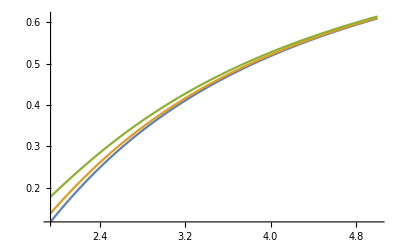

```mathematica
f[r_,Ω_,γ_] = 1-2/r(1+Ω/r^2+(Ω*γ)/r^3)^-1;
Plot[{f[r,0.6,0.1],f[r,0.7,0.1],f[r,0.9,0.12]},{r,1.94,5}]

FindRoot[f[r,0.,0]==0,{r,1}];(*Last command for getting event horizon radii*)
```

## Event horizon radii

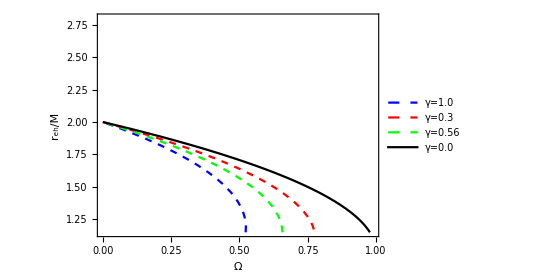

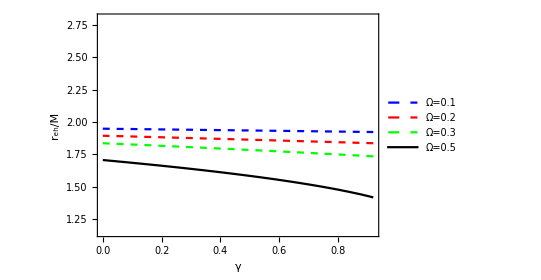

```mathematica
ContourPlot[{f[r,Ω,1]==0,f[r,Ω,0.3]==0,f[r,Ω,0.56]==0,f[r,Ω,0.]==0},{Ω,0,0.99},{r,1.15,2.8},ContourStyle->{{Dashed,Blue},{Dashed,Red},{Dashed,Green},{Black}},AspectRatio->0.7,Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},FrameLabel->{"Ω","r_eh/M"},PlotLegends->Placed[{"γ=1.0","γ=0.3","γ=0.56","γ=0.0"},{Scaled[{0.60,0.7}],{0,0.5}}]](* ! ! ! γ fixed for event horizon radii plot*)
ContourPlot[{f[r,0.1,γ]==0,f[r,0.2,γ]==0,f[r,0.3,γ]==0,f[r,0.5,γ]==0},{γ,0,0.92},{r,1.15,2.8},ContourStyle->{{Dashed,Blue},{Dashed,Red},{Dashed,Green},{Black}},AspectRatio->0.7,Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},FrameLabel->{"γ","r_eh/M"},PlotLegends->Placed[{"Ω=0.1","Ω=0.2","Ω=0.3","Ω=0.5"},{Scaled[{0.62,0.73}],{0,0.5}}]]
```

## Angular momentum and energy

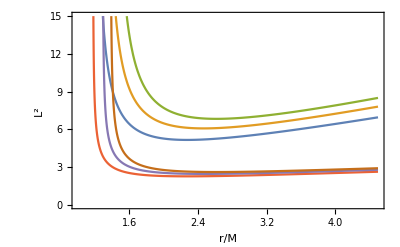

```mathematica
Ene = (-g[r,Q,a,α])/Sqrt[-g[r,Q,a,α] - r^2  *D[g[r,Q,a,α],r]/(2r)];//Simplify
L [r_,Q_,a_,α_]= (r^2 *Sqrt[(-D[g[r,Q,a,α],r])/(2 *r)])/Sqrt[-g[r,Q,a,α] - r^2  *D[g[r,Q,a,α],r]/(2r)];//Simplify

Plot[{L[r,0.3,0.5,-0.1]*L[r,0.3,0.5,-0.1],L[r,0.3,0.5,-0.2]*L[r,0.3,0.5,-0.2],L[r,0.3,0.5,-0.3]*L[r,0.3,0.5,-0.3],L[r,0.3,0.5,-0.1],L[r,0.3,0.5,-0.2],L[r,0.3,0.5,-0.3]},{r,1,4.5},Frame->True,FrameLabel->{"r/M ","L^2"},PlotRange->{{1,4.5},{0,15}}]
```

## Effective Potential

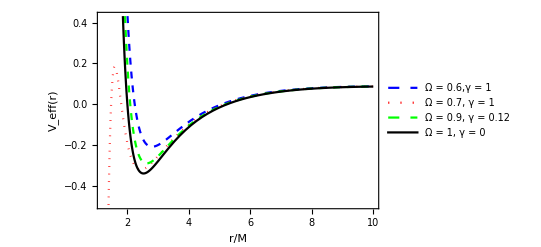

```mathematica
f[r_,Ω_,γ_] = 1-2/r(1+Ω/r^2+(Ω*γ)/r^3)^-1;
Veff[Ene_,L_,r_,Ω_,γ_]=-1 + Ene^2/f[r,Ω,γ]-L^2/r^2;
Plot[{Veff[1,4,r,0.6,1],Veff[1,4,r,0.7,1],Veff[1,4,r,0.9,0.12],Veff[1,4,r,1,0]},{r,1.2,10},FrameLabel->{"r/M","V_eff(r)","E/M=1","L/M=4"},Frame->True,LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotLegends->Placed[{"Ω = 0.6,γ = 1","Ω = 0.7, γ = 1","Ω = 0.9, γ = 0.12","Ω = 1, γ = 0"},{Scaled[{-0.12,0.25}],{-1.,0.5}}],PlotStyle->{{Dashed,Blue},{Dotted,Red},{Dashed,Green},{Black}}]
```

## ISCO radius